# Problem1

## 1. Harmonic oscillator

First of all, let us define h bar.

```mathematica
h=6.582119514*10^-16
```

6.58212×10^-16

You might want to write h bar like this:

```mathematica
ℏ
```

But this is bothering...

```mathematica
En[n_]:=h(n+1/2)
```

You may wonder what is the difference between = and :=.

```mathematica
En[1]
```

9.87318×10^-16

```mathematica
En[2]
```

1.64553×10^-15

```mathematica
En[-1]
```

-3.29106×10^-16

```mathematica
En[1/2]
```

6.58212×10^-16

Last two results imply that this code has some problems. That’s not what we want! Adding some constraint:

```mathematica
Energy[n_]:=h(n+1/2) /;n≥0
```

```mathematica
Energy[-2]
```

Energy[-2]

```mathematica
Energy[1]
```

9.87318×10^-16

```mathematica
Energy[1/2]
```

6.58212×10^-16

```mathematica
ClearAll[Energy]
```

```mathematica
Energy[n_Integer]:=h(n+1/2) /;n≥0
```

```mathematica
Energy[1]
```

9.87318×10^-16

```mathematica
Energy[-2]
```

Energy[-2]

```mathematica
Energy[1/2]
```

Energy[1/2]

## 2. Differentiation

With Mathematica, you can easily differentiate given functions. First, I will show you how to do.

```mathematica
D[x^2,x]
```

2 x

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[Tan[x],{x,2}]
```

2 Sec[x]^2 Tan[x]

```mathematica
D[Tan[x], {x,5}]
```

```mathematica
16 Sec[x]^6+88 Sec[x]^4 Tan[x]^2+16 Sec[x]^2 Tan[x]^4
```

```mathematica
D[Sin[x],x] /. x->0
```

1

```mathematica
D[x^2,x] /. x-> 0
```

0

```mathematica
D[Log[x],x]
```

1/x

```mathematica
D[Log[x],x] /. x-> 0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Diff[x_,t_]:=(Sin[x+t]-Sin[x])/t
```

```mathematica
Diff[0,0.0001]
```

1.

```mathematica
NumberForm[0.9999999983333334,16]
```

0.999999998333333

```mathematica
Diff[x_,t_]:=(Log[x+t]-Log[x])/t
```

```mathematica
Diff[2,0.0001]
```

0.499988

```mathematica
Diff[0,0.00000001]
```

∞

```mathematica
Diff[0,0.1]
```

∞

This is good time to introduce how to do integration.

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

Mathematica provide more intuitive way to make an order.

```mathematica
∫_0^π Sin[x]ⅆx
```

```mathematica
2
```

```mathematica
∫_0^π sin(x)ⅆx
```

2

```mathematica
∫x^x ⅆx
```

```mathematica
∫x^x ⅆx
```

```mathematica
∫_a^b ⅇ^(-x^2)ⅆx
```

1/2 √π (-Erf[a]+Erf[b])

## 3. Effective Sum

I want to introduce the List.

```mathematica
A={1,2,3}
```

```mathematica
{1,2,3}
```

```mathematica
A^2
```

{1,4,9}

```mathematica
f[x_]=x^2+1
```

1+x^2

```mathematica
f[A]
```

```mathematica
{2,5,10}
```

```mathematica
Table[10^6*i, {i,1,10^6}]
```

{1000000,2000000,3000000,4000000,5000000,6000000,7000000,8000000,9000000,10000000,11000000,12000000,13000000,14000000,999972,999987000000,999988000000,999989000000,999990000000,999991000000,999992000000,999993000000,999994000000,999995000000,999996000000,999997000000,999998000000,999999000000,1000000000000}
 |  |  |  |

```mathematica
Plus@@%
```

500000500000000000

```mathematica
For[t=0;
k=1, k≤ 10^6,k++,t+=k];Print[t]
```

500000500000

If you do not separate Print[t] on the code, you are going to face a disaster...

## 4. Basic Circle Plot with Tangent Line

```mathematica
Circle[{0,0},1]
```

Circle[{0,0},1]



```mathematica
Graphics[Circle[]]
```

```mathematica
Show[Graphics[Circle[{0,0}]],Axes->True,AxesStyle->Black]
```

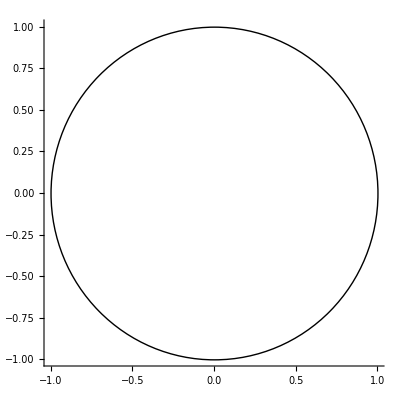

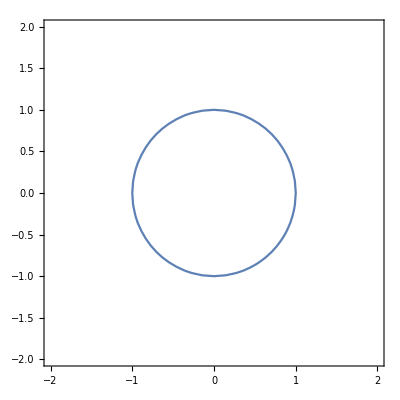

```mathematica
ContourPlot[x^2+y^2==1, {x,-2,2},{y,-2,2}, Axes->True]
```

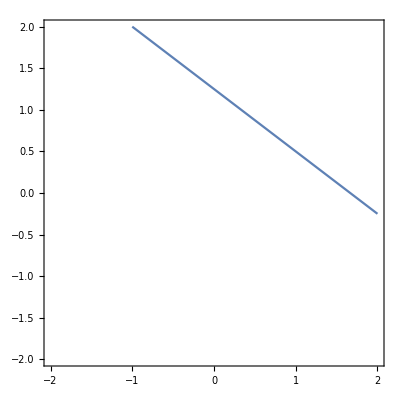

```mathematica
ContourPlot[3/5 x+4/5 y==1, {x,-2,2},{y,-2,2}]
```

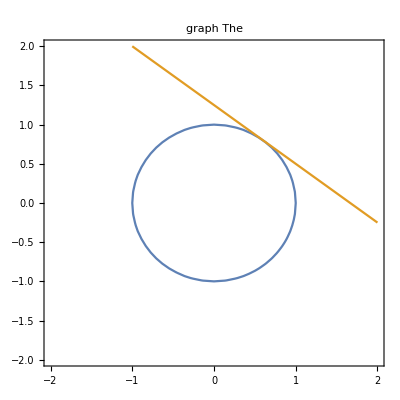

```mathematica
ContourPlot[{x^2+y^2==1,(3 x)/5+(4 y)/5==1},{x,-2,2},{y,-2,2},Axes->True, PlotLabel->The graph]
```

You can change the options for the plot easily.

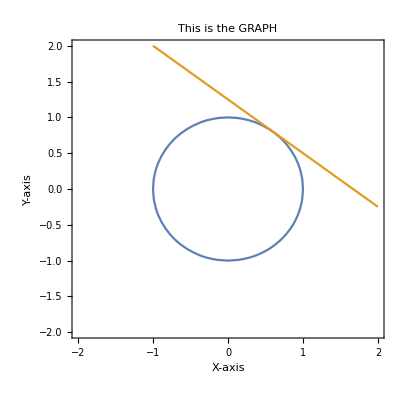

```mathematica
Show[%2,AxesLabel->{HoldForm[X-axis],HoldForm[Y-axis]},PlotLabel->HoldForm[This is the GRAPH],LabelStyle->{FontFamily->"AR BERKLEY",18,GrayLevel[0]}]
```